Star data

Import and display data

You’ve just been sent some signals to analyse from an undiscovered star. The data corresponds to normalized flux received by a space telescope. The data has a high noise content, but you’ve been tasked with recovering information about the periods present in the star.
1. The data has two columns: the first corresponds to Flux and the second to Time in days elapsed after an arbitrary start point. Plot the Time Series
2. Find the Fourier transform and estimate the power spectrum as the absolute value of the Fourier transform
3. Find the top 5 frequencies present in the data. Interpret the highest peak you get.
4. Divide the frequency of the next 4 peaks with the value of the frequency at the second highest peak 
5. Apply a mean filter of width .5 days, and check how it affects the time series and the Power spectrum
6. Apply a low pass filter for 2.5 day-1 and check how it affects the time series and the Power spectrum
7.  Apply a high pass filter for .25 day-1 and check how it affects the time series and the Power spectrum
8. Apply a band pass filter between the range .25 and 2.5 day-1 and check how it affects the time series and the Power spectrum

```mathematica
timeseries=Import[FileNameJoin[{NotebookDirectory[],"Kepler_flux_data_KIC_3440230.txt"}],"Table"];
```

```mathematica
timeseries//Dataset
```

```mathematica
flux = timeseries[[All,;;1]];
```

```mathematica
time = timeseries[[All,;;2]];
```

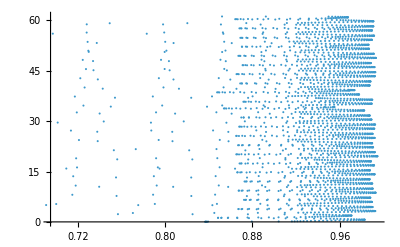

```mathematica
ListPlot[timeseries]
```